```mathematica
gray=RGBColor[0.7,0.7,0.7];
blue=Darker[RGBColor[0.48,0.8,1.]];
SetDirectory[NotebookDirectory[]];
```

## Figs A&B

```mathematica
firstElement[pairs_]:=(outFirst={};Do[AppendTo[outFirst,pairs[[iiMax]][[1]]],{iiMax,1,Length[pairs]}];
outFirst)
```

```mathematica
maxVal=firstElement[Import["IND_histograms//output//max//max_prob1_1_prob2_1_prob_cl_0_pd_0.026_.dat","Table"]];
giniVal=firstElement[Import["IND_histograms//output//gini//gini_prob1_1_prob2_1_prob_cl_0_pd_0.026_.dat","Table"]];
```

```mathematica
Mean[maxVal]
```

0.1333

```mathematica
Mean[giniVal]
```

0.616927

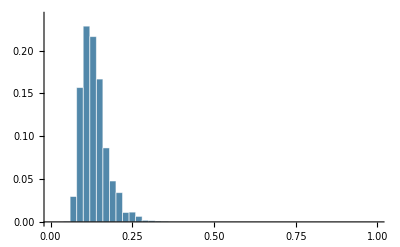

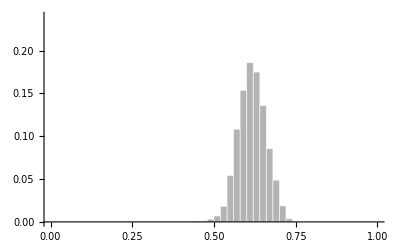

```mathematica
yMax=0.24;
opacity=0;
maxHistogram=Histogram[maxVal,10,"Probability",PlotRange->{{0,1},{0,yMax}},ChartStyle->blue,ChartBaseStyle->EdgeForm[{White,AbsoluteThickness[cm[0.02]]}]]
giniHistogram=Histogram[giniVal,10,"Probability",PlotRange->{{0,1},{0,yMax}},ChartStyle->gray,ChartBaseStyle->EdgeForm[{White,AbsoluteThickness[cm[0.02]]}]]
```

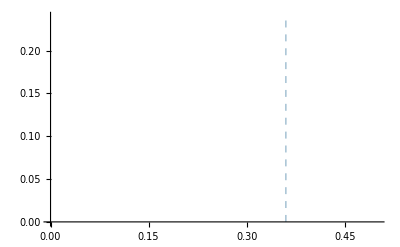

```mathematica
experimentMax=ListLinePlot[{
{{0.36,0},{0.36,yMax}}
},PlotRange->{{0,0.5},{0,yMax}},PlotStyle->{{blue,Dashed,AbsoluteThickness[cm[0.02]]}}]
```

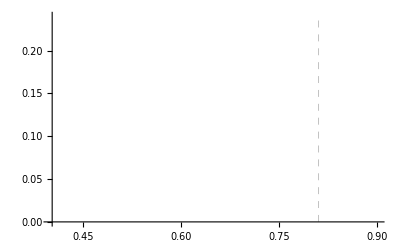

```mathematica
experimentGini=ListLinePlot[{
{{0.81,0},{0.81,yMax}}
},PlotRange->{{0.4,0.9},{0,yMax}},PlotStyle->{{gray,Dashed,AbsoluteThickness[cm[0.02]]}}]
```

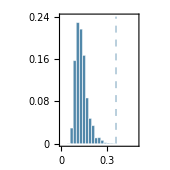

```mathematica
ρ=1;
margins={1.2,0.6,1.2,1.2};
figA=plotBack[
{experimentMax,maxHistogram},
xTicks->{0,0.1,0.2,0.3,0.4,0.5},
yTicks->{0,0.08,0.16,0.24},
tickLength->0.12,
plotRange->{{0,0.5},{0,0.24}},
plotDimensions->{3*6/5,3*6/5}*ρ,
plotMargins->margins*ρ,
plotLabels->{
Row[{Style["Largest cluster fractional size"]}],
Row[{Style["Probability"]}]},
labelsDistance->{0.5,0.9},
plotTitle->True,

titleText->Row[{Style["Independent Model"]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
```

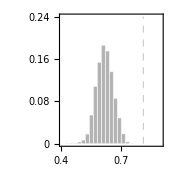

```mathematica
ρ=1;
margins={1.2,0.6,1.2,1.2};
figB=plotBack[
{experimentGini,giniHistogram},
xTicks->{0.4,0.5,0.6,0.7,0.8,0.9},
yTicks->{0,0.08,0.16,0.24},
tickLength->0.12,
plotRange->{{0.4,0.9},{0,0.24}},
plotDimensions->{3*6/5,3*6/5}*ρ,
plotMargins->margins*ρ,
plotLabels->{
Row[{Style["Gini coefficient "],Style["G",Italic]}],
Row[{Style["Probability"]}]},
labelsDistance->{0.5,0.9,0.9},
plotTitle->True,

titleText->Row[{Style["Independent Model"]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
```

```mathematica
t1=Rotate[Style["Experiment",FontSize->7,FontFamily->"Arial",gray],90°];
t2=Rotate[Style["Experiment",FontSize->7,FontFamily->"Arial",blue],90°];
```

```mathematica
FigA=figure[6,5,
elements->{figA,t2},
elementCoordinates->{
{0,0},
{1.2+3*6/5*(0.36)/0.5+0.3,-0.6-(0.5)*3*6/5}
},
centeredElements->{2,3}]
```

-Graphics-

```mathematica
FigB=figure[6,5,
elements->{figB,t1},
elementCoordinates->{
{0,0},
{1.2+3*6/5*(0.41)/0.5+0.3,-0.6-(0.5)*3*6/5}
},
centeredElements->{2,3}]
```

-Graphics-

## Fig C

```mathematica
pointsGini={};
pointsFraction={};
errorsGini={};
errorsFraction={};
sigList={0.01,0.02,0.05,0.1,0.2,0.5,1,2,5,10};
Do[
sig=sigList[[iiSig]];
Print["CCT//output//diversity//diversity_t1_9.6_sig1_"<>ToString[sig]<>"_t0r_1_sig2_"<>ToString[sig]<>"_prob_0_pd_0.026_.dat"];
divV=Import["CCT//output//diversity//diversity_t1_9.6_sig1_"<>ToString[sig]<>"_t0r_1_sig2_"<>ToString[sig]<>"_prob_0_pd_0.026_.dat","Table"];
nnn=divV[[1001]][[-1]];
AppendTo[pointsGini,{{Log[sig],divV[[1001]][[2]]},ErrorBar[divV[[1001]][[3]]*√(nnn/(nnn-1))]}];
AppendTo[pointsFraction,{{Log[sig],divV[[1001]][[16]]},ErrorBar[divV[[1001]][[17]]*√(nnn/(nnn-1))]}];
,{iiSig,1,Length[sigList]}];
```

CCT//output//diversity//diversity_t1_9.6_sig1_0.01_t0r_1_sig2_0.01_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_0.02_t0r_1_sig2_0.02_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_0.05_t0r_1_sig2_0.05_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_0.1_t0r_1_sig2_0.1_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_0.2_t0r_1_sig2_0.2_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_0.5_t0r_1_sig2_0.5_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_1_t0r_1_sig2_1_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_2_t0r_1_sig2_2_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_5_t0r_1_sig2_5_prob_0_pd_0.026_.dat

CCT//output//diversity//diversity_t1_9.6_sig1_10_t0r_1_sig2_10_prob_0_pd_0.026_.dat

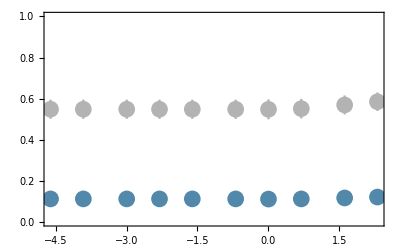

```mathematica
b1=ErrorListPlot[pointsGini,PlotRange->{Log[{0.01,10}],{0,1}},PlotStyle->{gray,PointSize->0.03}];
b2=ErrorListPlot[pointsFraction,PlotRange->{Log[{0.01,5}],{0,1}},PlotStyle->{blue,PointSize->0.03}];
bTheory=Show[{b1,b2},PlotRange->{Log[{0.01,10}],{0,1}},Frame->True]
```

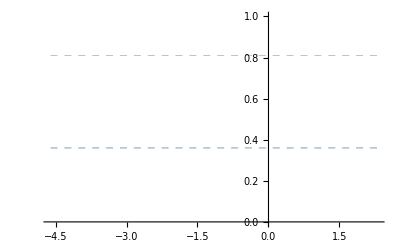

```mathematica
bExperiment=ListLinePlot[{
{{Log[0.01],0.81},{Log[10],0.81}},
{{Log[0.01],0.36},{Log[10],0.36}}
},PlotRange->{Log[{0.01,10}],{0,1}},PlotStyle->{{gray,Dashed,AbsoluteThickness[cm[0.02]]},{blue,Dashed,AbsoluteThickness[cm[0.02]]}},
PlotRange->{{Log[0.01],Log[10]},{0,1}}
]
```

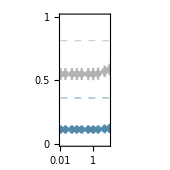

```mathematica
figC=plotTwoLegends[
{bExperiment,bTheory},
xTicks->Log[{0.01,0.1,1,10}],
xReplace->{0.01,0.1,1,10},
yTicks->{0,0.25,0.5,0.75,1},
yTicks2->{0,0.25,0.5,0.75,1},
tickLength->0.12,
plotRange->{Log[{0.01,10}],{0,1}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.2,0.6,1.2,1.2},
plotLabels->{
Row[{Style["Standard deviation "],Subscript[Style["σ"],Style["0",FontSize->5]],Style[" [h]"]}],
Row[{Style["Largest cluster fractional size",blue]}],Row[{Style["Gini coefficient ",gray],Style["G",Italic,gray]}]},
labelsDistance->{0.5,0.9,0.9},
plotTitle->True,
titleText->Row[{Style["Cell Cycle Timer ("],Subscript[Style["t",Italic],Style["0",FontSize->5]],Style[" = 9.6 h)"]}],
titleDistance->0.25,
leftColor->blue,
rightColor->gray,
fontMain->7,
fontName->"Helvetica"
]
```

```mathematica
t1=Style["Experiment (Gini)",FontSize->7,FontFamily->"Arial",gray]
t2=Style["Experiment (Larg. fraction)",FontSize->7,FontFamily->"Arial",blue]
```

Experiment (Gini)

Experiment (Larg. fraction)

```mathematica
FigC=figure[6,5,
elements->{figC,t1,t2},
elementCoordinates->{
{0,0},
{1.2+3*6/5*1/2,-0.6-(1-0.81)*3*6/5-0.3},
{1.2+3*6/5*1/2,-0.6-(1-0.36)*3*6/5-0.3}
},
centeredElements->{2,3}]
```

-Graphics-

## Figure

```mathematica
x0=0;
y0=0;
dx=5.2;
dy=-5.2;
dy2=-1;
dL=0.1;
y1=-5.1;
FigED2=figure[16.5,5.2,
elements->{
FigA,FigB,FigC
},
elementCoordinates->{
{x0,y0},{dx+x0,y0},{2*dx+x0,y0}
},
letters->{
Style["a",FontFamily->"Helvetica",Bold,FontSize->8],
Style["b",FontFamily->"Helvetica",Bold,FontSize->8],
Style["c",FontFamily->"Helvetica",Bold,FontSize->8]
},
letterCoordinates->{
{x0,y0},{dx+x0,y0},{2*dx+x0,y0}
}]
```

-Graphics-

```mathematica
Export["figs//SYS_ED_Fig3.pdf",FigED2]
```

figs//SYS_ED_Fig3.pdf